# C&Q Chaos I - Intro to Mathematica and dynamical systems

In this lecture we will briefly introduce Mathematica and its capabilities as needed in this course. This is not meant to be a complete introduction, but mainly a “crash course”, so that you are able to fully understand what is being done in the notebooks we will go through during the lectures. (A broader crash course is provided by Wolfram here: https://www.wolfram.com/language/fast-introduction-for-math-students/en/ )

In your closing project, you can use any other software or language. 

We encourage qualified use of AI to write and analyse code (Claude, Gemini, ChatGPT, or a local LLM running on your computer), we want you to be able to go and investigate the dynamics of a systems by any means possible. (Image below is a ChatGPT text-to-image of the title of this notebook.)

-Graphics-
The second part of the notebook will also seamlessly introduce the concept of dynamical systems and how to model them in Mathematica. This mostly means deriving Hamilton’s equations of motion, integrating them, and visualizing the output in reasonable ways.

## Mathematica elements

## Formatting, Input, Output

- The formatting of the sections you see in this notebook is done through Format>Style>... 
 - There are also keyboard shortcuts Alt+Number (Cmd+Number on Mac) that you can learn if you write in Mathematica often. 
 - You can open and close section groups using the elements on the right or Ctrl+‘ (Cmd+‘ on Mac). 
 - Ctrl+Shift+D (Cmd+Shift+D) starts a new Cell.
  - Alt/Cmd+9 makes it an Input cell. Input Cells can be evaluated by pressing Shift+Enter (similar to Jupyter notebooks).
  - Shortcuts can make your life easier, see “tutorial/KeyboardShortcutListing” in Help>Documentation

```mathematica
x=3; (*Semi-colon suppresses output*)
x^2 (*Press Ctr+^ for upper index*)
Clear[x](*After this command, the variable x has no definition and Mathematica sees is simply as a symbol.*)
x^2
```

9

0

x^2

```mathematica
%^2(*Percent symbol accesses last output *anywhere*. This can be dangerous. Try evaluating twice to find out why*)
```

x^8

```mathematica
(*It is safer to store outputs in variables and do operations on them.*)
```

## Functions, plots

One of the powers of Mathematica is its huge library of optimized functions. Usually you write them as Function[Arguments, Options]. 
Pro Tip: If there is a Mathematica function for something, it usually does it better/more optimally than any implementation you can come up with.

```mathematica
x=3
Sin[x] (*By default, Mathematica tries to keep results exact if given exact numbers.*)
N[Sin[x]](*N[] forces numerical evaluation.*)
Sin[3.](*Giving a float switches a function into numerical mode.*)
FullForm[Sin[3.]] (*Output shows fewer digits than it really knows. FullForm[] forces Mathematica to tell you everything.*)
```

3

Sin[3]

0.14112

0.14112

0.14112

```mathematica
(*Define your own function.*)
f[x_]:= x^2; (*Mathematica understands x as an internal variable.*)
f[x]
```

Pro Tip: Mathematica has one of the best documentations ever. Make sure to use it. Go to Help>Documentation and search for anything. For basic info and examples you will get better answers than searching discussion fora such as StackExchange.

```mathematica
(*Try typing the beginning of a name of a function and looking up the Documentation by clicking on the "i" button.*)
-Graphics-;
```

Mathematica has rich possibilities of plotting, even though it takes time if you want to format the output exactly.

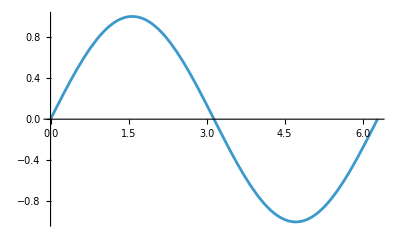

```mathematica
(*Plotting a simple function.*)
Plot[Sin[x],{x,0,2π}] (*Mathematica now implicitly understands that x is an internal variable.*)
```

```mathematica
(*Plotting a potential in 2D.*)
ContourPlot[Sin[x^2+2 y^2],{x,-π,π},{y,-π,π}]
Plot3D[Sin[x^2+2 y^2],{x,-π,π},{y,-π,π},MaxRecursion->6] (*MaxRecursion option asks Mathematica to refine the plot.*)
```

-Graphics-

-Graphics3D-

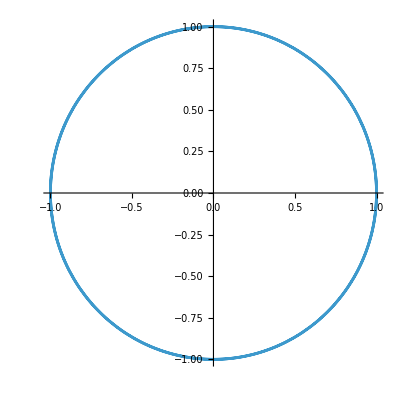

-Graphics3D-

```mathematica
(*Parametric plots are great for trajectories.*)
ParametricPlot[{Sin[p],Cos[p]},{p,0,4π}]
ParametricPlot3D[{Sin[p],Cos[p],p},{p,0,4π}]
```

## Wrangling expressions

Many of the capabilities of Mathematica have gradually been shadowed in Python+Jupyter in the past 10 years. However, Mathematica still dominates in symbolic computations. Here are some of the tips to get started.

```mathematica
(*There is more than one way to write the same thing in Mathematica.*)
Power[x,2]
x^2
x^2
```

```mathematica
(*Functions can be applied also in more than one way.*)
Sin@x
Sin[x]
x//Sin
```

```mathematica
(*Pure functions are like lambda functions in Python.*)
```

```mathematica
f = #^2&
f[x]
```

```mathematica
(*You can apply a pure function in the ways as Sin above!*)
#^2&@x
x//#^2&
#^2&[x]
```

```mathematica
(*No need to understand this now, just look this up if you see #, &, //, or @ in an expression.*)
(*Look up tutorial/OperatorInputForms in the documentation if you want to go hardcore.*)
```

```mathematica
(*One of the often used functions is Simplify and FullSimplify. It tries to make the expression "simple" by Mathematica criteria. This is not perfect for long expressions, but great in most cases.*)

polynom = ExpandAll[(y^2-2)^3] (*Expands the expression into monomials*)
```

-8+12 y^2-6 y^4+y^6

```mathematica
Simplify[polynom]
FullSimplify[polynom]
(*FullSimplify knows identities involving special functions, generally the output is comparable to Simplify but slower.*)
Cosh[y]+Sinh[y]//Simplify
Cosh[y]+Sinh[y]//FullSimplify
```

(-2+y^2)^3

(-2+y^2)^3

Cosh[y]+Sinh[y]

ⅇ^y

```mathematica
(*Assumptions can be given*)
Simplify[√((y-a)^2)]
Simplify[√((y-a)^2),{y>a}]
Simplify[√((y-a)^2),{y<a}]
```

Solutions of differential and algebraic equations are returned as a list of “Rules” (->). You can apply them using the command ReplaceAll (/.)

```mathematica
ysol =Solve[a y^2 - b y + c==0,y]
```

```mathematica
(*You can access elements of a list  by [[N]]. Lists are numbered starting from 1!*)
y/.ysol[[1]]
y/.ysol[[2]]
```

```mathematica
(*Mathematica automatically "Threads" most operations (applies operations to every element of the list) when given lists.*)
```

```mathematica
a y^2 - b y + c/.ysol
%//Simplify
```

## Deterministic dynamical systems

Informally: given an initial condition, a deterministic dynamical system evolves into a unique state that was fully determined by the initial condition.
- In classical physics, we mostly deal with continuous dynamical systems. There we typically have a state vector and a differential equation governing it.
- In other areas of science (such as population biology), one sometimes employs discrete dynamical systems. The steps of the dynamical system may, for instance, refer to generations of the evolving population.

## Discrete systems

Discrete systems are characterized by some state vector. The next step (or iteration) of such a discrete system is given by a known map. Below we first discuss one of the simplest maps used in epidemiology and population dynamics. Then we go to the second example, which allows to “discretize” a continuous evolution. This example will be a key method for the first half in this course, so it is important that you understand it in detail.

### Reproduction number

Consider the population where in a characteristic time, an individual gives birth to "r" other individuals and ceases to exist . Find the list of populations for 20 generations, starting from 1 individual and a reproduction number equal to 2.

#### Define “pop” as the function that gives the current population given the previous population “lastpop” and the reproduction number “r” as arguments:

#### Show solution

```mathematica
pop[lastpop_,r_]:=r lastpop;
```

#### Given this iterator, create a list of the population evolution for 20 generations using Table[]

```mathematica
(*You can use any initial population and value of "r"*)
```

#### Show solution

```mathematica
(*Mathematica creates lists by the function Table*)
popEvol = Table[1,{i,1,20}];
Table[popEvol[[i]] = pop[popEvol[[i-1]],2],{i,2,20}] (*It is better to use Table as iterators than For loops in Mathematica!*)
```

{2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768,65536,131072,262144,524288}

#### Plot the time series using ListPlot[]

#### Show solution

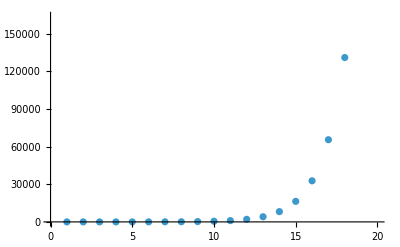

```mathematica
ListPlot[popEvol]
```

### Discrete system as a snapshot of a continuous model

Say you know the general solution for the evolution of a continuous model. Here we consider motion on a circle.

```mathematica
xc[t_] := R Sin[t-t0];
yc[t_] := R Cos[t-t0];
(*R and t0 are determined by initial conditions.*)
R=1;t0=0;
ParametricPlot[{xc[t],yc[t]},{t,0,2 π}]
Clear[R,t0]
```

How to describe it as a discrete dynamical system that evolves to a next instant shifted by Δt? (Given a previous state, give the next one with t+Δt.)

#### Say you observe the system at some values of x, y. Figure out what is t - t0 and R given your knowledge of the general solution for the evolution. Write a function using Module[] that uses this information to generate the next point .

#### Show solution

```mathematica
(*Iterator NextPoint finds the phase of the system and R, then gives the next point.*)
NextPoint[x0_,y0_,Δt_] := Module[{tmt0,R},
R = √(x0^2+y0^2);
tmt0 = ArcTan[y0,x0]; (*The two-argument function evaluates arctan(x0/y0), using two arguments makes the function stable as y0 is close to zero.]*)
{R Sin[tmt0 + Δt],R Cos[tmt0 + Δt]}
]
```

#### Generate a list of 100 iterations and plot the result

#### Show solution

```mathematica
(*Generate a list of values*)
xyList = Table[{1.,0},{i,1,100}];
Table[xyList[[i]]=NextPoint[xyList[[i-1,1]],xyList[[i-1,2]],1],{i,2,100}];
(*The period of the system is 2π, so Δt=1 never manages to close the loop, it will asymptotically sample the circle.*)
ListPlot[xyList,AspectRatio->1]
```

#### Use Manipulate[] and Take[] to visualize the evolution of the snapshots as more iterations are added

#### Show solution

```mathematica
Manipulate[ListPlot[Take[xyList,n],AspectRatio->1,PlotRange->{{-1,1},{-1,1}}],{n,1,100,1}]
```

## Continuous systems

Continuous systems are also characterized by a state vector x. (The vector x generally does not refer to spatial coordinates here.) The dynamics are specified by giving a first-order ODE specifying the time-derivative of x. (If more time-derivatives exist, we can formally introduce more dimensions to the state space and identify the higher time derivatives with the new variables.)

In Hamiltonian systems, the state vectors are the coordinates and momenta q^j,p_i, i=1,...N, and they span the 2N-dimensional phase space. However, it is good to remember that x does not need to generally have a mechanical interpretation. It can also include variables such as temperature or ratios of chemical compounds, certain moments of a PDE, etc.

### Harmonic oscillator

```mathematica
H[p_,x_] := 1/2(p^2 + x^2); 
(*We simplify the description by using units where m=k=1.*)
(*As a consequence, period will be 2π*)
```

#### Derive Hamilton’s equations of motion using the derivative function D[]. State them as ODEs for x[t], p[t] as a list of equations with “==”.

#### Show solution

```mathematica
Clear[x]
EOM = {x'[t]==(D[H[p,x],p]/.{x->x[t],p->p[t]}),p'[t] == (-D[H[p,x],x]/.{x->x[t],p->p[t]})}
```

#### Solve the equations given some initial conditions using NDSolve[]

#### Show solution

```mathematica
Init ={x[0] == 1,p[0]==0} ; (*Initial conditions, NDSolve takes them as part of the equations to be solved*)
Evolution =NDSolve[Join[EOM,Init],{x[t],p[t]},{t,0,10}] (*Join merges two lists*)
```

#### Plot x as a function of t, show trajectory in phase space x(t), p(t)

#### Show solution

```mathematica
Plot[x[t]/.Evolution[[1]],{t,0,10}]
ParametricPlot[{x[t],p[t]}/.Evolution[[1]],{t,0,10}]
```

#### Plot energy levels in phase space, find energy of above initial conditions and plot single contour corresponding to that energy

#### Show solution

```mathematica
ContourPlot[H[p,x],{x,-1,1},{p,-1,1}] (*Contour plot of all energy levels.*)
E0 = H[0,1] (*Energy of initial conditions above.*)
ContourPlot[H[p,x]==E0,{x,-1,1},{p,-1,1}] (*In this case (autonomous Hamiltonian system with 1 degree of freedom) we were able to find the shape of the trajectory in phase space by finding the energy hypersurface.*)
```

#### Express x’[t] as a function of x using the energy conservation

#### Show solution

```mathematica
(*Express p as a function of x*)
psol = Solve[En == H[x[t],p[t]],p[t]]
(*Both branches are relevant for some part of the motion*)
ReducedEOM = EOM[[1]]/.psol
```

#### Advanced wrangling: Find the general solution for x[t] in a reasonable form. (DSolve[])

This is a simple example which is overkill to do with Mathematica in this way, but the same approach can be used also for other systems.

#### Show solution

```mathematica
(*We can try DSolve for the positive branch*)
Evol = DSolve[ReducedEOM[[2]],x[t],t]
(*This gives multiple solutions*)
```

```mathematica
(*Which solution is correct given reasonable assumptions?*)
D[(x[t]/.Evol),t]  -(√(2 En-x[t]^2)/.Evol)//FullSimplify[#,{t ∈ Reals,C[1]∈ Reals}]& (*Note the assumptions in FullSimplify!*)
(*It turns that the second solution is correct under niceness assumptions*)
```

```mathematica
(*This is what we wrangled out of Mathematica so far*)
```

```mathematica
CorrectEvol = FullSimplify[Evol[[2]],{t ∈ Reals,C[1]∈ Reals}]
```

```mathematica
(*There are annoying branch cuts, we can simplify to a smooth function in one interval and use that on the rest of the interval by smoothness/analytical extension arguments. (The differential equation is smooth, so there is no reason for the solution to be non-smooth.)*)
ExtEvol = {x[t]->Simplify[x[t]/.CorrectEvol,{0<t+C[1]<π/2}]}
```

```mathematica
(*In this simple case Mathematica would even be able to find the general solution on its own from the EOM using DSolve. In other cases one would have to help it.*)
DSolve[EOM,{x[t],p[t]},t]
```

### Mathematical pendulum and unstable equilibria

```mathematica
-Graphics-;
Clear[H]
H[p_,x_] := 1/2 p^2 - Cos[x];
(*Again special units for simplicity. The phase-space is 2π-periodic in x. x=0 is the equilibrium position, x=±π is the upright position.*)
```

#### Repurpose your code above to briefly explore the mathematical pendulum

#### Show solution

```mathematica
EOM = {x'[t]==(D[H[p,x],p]/.{x->x[t],p->p[t]}),p'[t] == (-D[H[p,x],x]/.{x->x[t],p->p[t]})}
x0 = 2.5; 
p0=0;
Init ={x[0] == x0,p[0]==p0} ;
Evolution =NDSolve[Join[EOM,Init],{x[t],p[t]},{t,0,20}]
Plot[x[t]/.Evolution[[1]],{t,0,10}]
ParametricPlot[{x[t],p[t]}/.Evolution[[1]],{t,0,15}]
ContourPlot[H[p,x],{x,-π,π},{p,-π,π},Contours->20] (*Contour plot of all energy levels.*)
E0 = H[p0,x0] (*Energy of initial conditions above.*)
ContourPlot[H[p,x]==E0,{x,-π,π},{p,-π,π}] (*In this case (autonomous Hamiltonian system with 1 degree of freedom) we were able to find the shape of the trajectory in phase space by finding the energy hypersurface.*)
```

#### Assume you don’t know anything about the function Cos[x]. Classify the extrema of the potential on the interval x ∈ [-π,π], find the corresponding energies.

#### Show solution

```mathematica
(*There are several ways to do this. Below is the analytical approach.*)
V[x_]:=-Cos[x];
extrema = Solve[D[V[x],x]==0&&-π<=x<=π,x]
(*Note that x=π and x=-π correspond to the same point!*)
Energies = V[x]/.extrema
```

#### Expand potential around the maximum up to δx^2 using Series[] (and truncate using Normal[]).

#### Show solution

```mathematica
VSer = Series[V[π+δx],{δx,0,2}]
VTrunc = Normal[VSer]
(*The two outputs may not look that different, but VSer is a "SeriesData[]" object, VTrunc is a normal expression.*)
FullForm[VSer]
FullForm[VTrunc]
```

#### Find equations of motion for the particle at the unstable energy near the potential.

#### Show solution

```mathematica
Htrunc[δp_,δx_]:= 1/2 δp^2 + 1-δx^2/2;
TrajRule = {δx->δx[t],δp->δp[t]}; (*To avoid writing it twice*)
EOMtrunc = {δx'[t]==(D[Htrunc[δp,δx],δp]/.TrajRule ),δp'[t]==-(D[Htrunc[δp,δx],δx]/.TrajRule )}
```

#### Solve the approximate equations of motion for general initial conditions

#### Show solution

```mathematica
(*Let's try DSolve*)
truncSol = DSolve[Join[EOMtrunc,{δp[0]==δp0,δx[0]==δx0}],{δx[t],δp[t]},t]
truncSol//ExpandAll
Collect[%,ⅇ^t]
```

#### Generate a list of rules for a number of initial conditions within a circle of some radius from δp=0, δx=0 and visualize them

#### Show solution

```mathematica
InitConds = Table[{δp0->0.01j Sin[i π/8],δx0->0.01j Cos[i π/8]},{i,1,16},{j,1,4}]
(*Visualize initial conditions*)
ListPlot[{δp0,δx0}/.InitConds,AspectRatio->1, AxesLabel->{δp0,δx0}]
```

#### Plot the evolutions given the initial conditions from above. (Bonus: overlay the evolutions with the original initial conditions by using Show[].)

#### Show solution

```mathematica
truncEvols = truncSol[[1]]/.InitConds;
(*show one row:*)
truncEvols[[2]]
```

```mathematica
Show[ParametricPlot[{δp[t],δx[t]}/.truncEvols,{t,0,1},AspectRatio->1, AxesLabel->{δp,δx}],ListPlot[{δp0,δx0}/.InitConds,AspectRatio->1, AxesLabel->{δp0,δx0},PlotStyle->Red]]
```

#### More on the unstable equilibrium

```mathematica
(*Obviously there are stable and unstable directions*)
 truncSol[[1]]/.{δp0->a,δx0->a}
 truncSol[[1]]/.{δp0->-a,δx0->a}
(*Unless you exactly hit the condition δp0 == -δx0, the exponentially growing solution will always be represented and it will quickly dominate. *)
```

The point δx0 = δp0 = 0 is an unstable fixed point of the system . The full non - truncated prolongations of the δp0 == -δx0 manifold is the stable manifold of the fixed point . The δp0 == δx0 prolongation would be known as the unstable manifold of the fixed point. The formal definition is that the points on the stable/unstable manifold approach the fixed point as t-> ±∞. 

For the mathematical pendulum these appear along E=1.  Interestingly enough, the full unstable/stable manifolds are the same under the periodic identification! This is known as a homoclinic manifold (a manifold whose points evolve to the same fixed point as both t-> ±∞.)

```mathematica
ContourPlot[H[p,x]==1,{x,-π,π},{p,-π,π}]
```

## Sandbox